```mathematica
n=6
b=2
a=-2
h=(b-a)/n
XDT={};YDT={};
For[i=0,i≤n,i++,
xdata[i]=a+i×h;
ydata[i]=N[Exp[-xdata[i]]];
XDT=Append[XDT,xdata[i]];
YDT=Append[YDT,ydata[i]];];
Array[xdata,{n+1,0}];
Array[ydata,{n+1,0}];
MatrixForm[XDT]MatrixForm[YDT]
```

```mathematica
({{-2}, {-4/3}, {-2/3}, {0}, {2/3}, {4/3}, {2}}) ({{7.38905609893065}, {3.7936678946831774}, {1.9477340410546757}, {1.}, {0.513417119032592}, {0.26359713811572677}, {0.1353352832366127}})
```

```mathematica
Array[difftab,{n+1,n+1},{0,0}];
For[k=1,k≤n,k++,
For[i=n,i≥n-k,i--,difftab[i,k]=""]];
For[i=0,i≤n,i++,difftab[i,0]=ydata[i]];
For [k=1, k≤n,k++,
For[i=0,i≤n-k,i++,
difftab[i,k]=(difftab[i+1,k-1]-difftab[i,k-1])/(xdata[i+k]-xdata[i])]];
tab1 = Array[difftab,{n+1,n+1}, {0,0}];
PaddedForm[TableForm[tab1],{6,5}]
```

7.38906 | -5.39308 |  1.96814 | -0.47883 |  0.08737 | -0.01275 |  0.00155
 3.79367 | -2.76890 |  1.01047 | -0.24584 |  0.04486 | -0.00655 | 
 1.94773 | -1.42160 |  0.51880 | -0.12622 |  0.02303 |  | 
 1.00000 | -0.72987 |  0.26636 | -0.06480 |  |  | 
 0.51342 | -0.37473 |  0.13675 |  |  |  | 
 0.26360 | -0.19239 |  |  |  |  | 
 0.13534 |  |  |  |  |  |

```mathematica
pln = difftab[0,0]+difftab[0,1]×(x-xdata[0]);
n=6;lst=List[pln];
For[k=2,k≤n,k++,
pln=lst[[k-1]]+difftab[0,k]×∏_(i=0)^(k-1) (x-xdata[i]);
lst=Append[lst,pln]];
nwtn[x_]:=N[lst[[n]]];
ColumnForm[lst]
```

7.38906-5.39308 (2+x)
7.38906-5.39308 (2+x)+1.96814 (4/3+x) (2+x)
7.38906-5.39308 (2+x)+1.96814 (4/3+x) (2+x)-0.478831 (2/3+x) (4/3+x) (2+x)
7.38906-5.39308 (2+x)+1.96814 (4/3+x) (2+x)-0.478831 (2/3+x) (4/3+x) (2+x)+0.0873716 x (2/3+x) (4/3+x) (2+x)
7.38906-5.39308 (2+x)+1.96814 (4/3+x) (2+x)-0.478831 (2/3+x) (4/3+x) (2+x)+0.0873716 x (2/3+x) (4/3+x) (2+x)-0.0127541 (-2/3+x) x (2/3+x) (4/3+x) (2+x)
7.38906-5.39308 (2+x)+1.96814 (4/3+x) (2+x)-0.478831 (2/3+x) (4/3+x) (2+x)+0.0873716 x (2/3+x) (4/3+x) (2+x)-0.0127541 (-2/3+x) x (2/3+x) (4/3+x) (2+x)+0.00155148 (-4/3+x) (-2/3+x) x (2/3+x) (4/3+x) (2+x)

```mathematica
ColumnForm[Collect[lst,x]]
```

-3.39711-5.39308 x
1.85125+1.16737 x+1.96814 x^2
1.-1.17358 x+0.0528134 x^2-0.478831 x^3
1.-1.01825 x+0.479963 x^2-0.129344 x^3+0.0873716 x^4
1.-1.00314 x+0.498858 x^2-0.157687 x^3+0.0448581 x^4-0.0127541 x^5
1.-1.00068 x+0.500084 x^2-0.164582 x^3+0.0414103 x^4-0.0096511 x^5+0.00155148 x^6

```mathematica
data = {{-2,7.38905609893065},{-4/3,3.7936678946831774},{-2/3,1.9477340410546757},{0,1.},{2/3,0.513417119032592}{4/3,0.26359713811572677},{2,0.1353352832366127}}
inpln:=InterpolatingPolynomial[data,x];
Collect[inpln,x]
```

{{-2,7.38906},{-4/3,3.79367},{-2/3,1.94773},{0,1.},{8/9,0.135335},{2,0.135335}}

1.-1.10507 x+0.270728 x^2-0.24351 x^3+0.104955 x^4+0.0166051 x^5

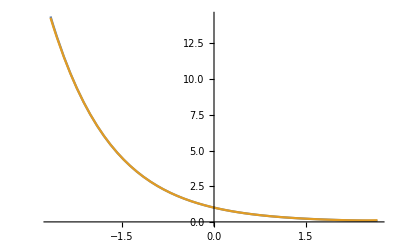

```mathematica
Plot[{Exp[-x],nwtn[x_]},{x,a-h,b+h}]
```

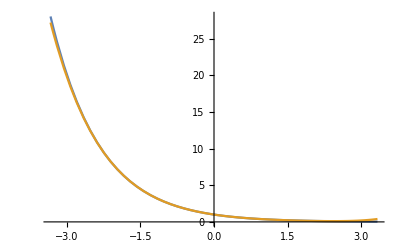

```mathematica
Plot[{Exp[-x],nwtn[x_]},{x,a-2h,b+2h}]
```

```mathematica
Pln={};P[n+1]=0;
For[i=n,i≥0,i--,P[i]=difftab[0,i]+(x-xdata[i])P[i+1];
Pln=Append[Pln,P[i]];]
ColumnForm[Pln]
```

0.00155148
-0.0127541+0.00155148 (-4/3+x)
0.0873716+(-0.0127541+0.00155148 (-4/3+x)) (-2/3+x)
-0.478831+(0.0873716+(-0.0127541+0.00155148 (-4/3+x)) (-2/3+x)) x
1.96814+(2/3+x) (-0.478831+(0.0873716+(-0.0127541+0.00155148 (-4/3+x)) (-2/3+x)) x)
-5.39308+(4/3+x) (1.96814+(2/3+x) (-0.478831+(0.0873716+(-0.0127541+0.00155148 (-4/3+x)) (-2/3+x)) x))
7.38906+(2+x) (-5.39308+(4/3+x) (1.96814+(2/3+x) (-0.478831+(0.0873716+(-0.0127541+0.00155148 (-4/3+x)) (-2/3+x)) x)))

```mathematica
P[0]
```

7.38906+(2+x) (-5.39308+(4/3+x) (1.96814+(2/3+x) (-0.478831+(0.0873716+(-0.0127541+0.00155148 (-(4/3)+x)) (-(2/3)+x)) x)))

```mathematica
nwtn[x_]:=P[0];
m=60
XDAT={};YDAT={};nwtnDAT={};MR={};
For[i=0,i≤m,i++,
xdatas[i]=a+i×(h/10);
ydatas[i]=N[Exp[-xdatas[i]]];
x=xdatas[i];
nwtndatas[i]=nwtn[i];
mr[i]=Abs[ydatas[i]-nwtndatas[i]];
XDAT=Append[XDAT,xdatas[i]];
YDAT=Append[YDAT, ydatas[i]];
nwtnDAT=Append[nwtnDAT,nwtndatas[i]];
MR=Append[MR,mr[i]];];
MatrixForm[N[XDAT]]MatrixForm[N[YDAT]]MatrixForm[N[nwtnDAT]]MatrixForm[MR]
```

60

(-2.
-1.93333
-1.86667
-1.8
-1.73333
-1.66667
-1.6
-1.53333
-1.46667
-1.4
-1.33333
-1.26667
-1.2
-1.13333
-1.06667
-1.
-0.933333
-0.866667
-0.8
-0.733333
-0.666667
-0.6
-0.533333
-0.466667
-0.4
-0.333333
-0.266667
-0.2
-0.133333
-0.0666667
0.
0.0666667
0.133333
0.2
0.266667
0.333333
0.4
0.466667
0.533333
0.6
0.666667
0.733333
0.8
0.866667
0.933333
1.
1.06667
1.13333
1.2
1.26667
1.33333
1.4
1.46667
1.53333
1.6
1.66667
1.73333
1.8
1.86667
1.93333
2.) (0.
0.000919918
0.00138973
0.00154117
0.00147892
0.00128464
0.00102059
0.000732754
0.000453733
0.000205181
4.44089×10^-16
0.00015577
0.000261318
0.000319663
0.000336466
0.000319043
0.000275546
0.000214301
0.000143297
0.0000697842
8.88178×10^-16
0.0000610207
0.000109543
0.000143158
0.000160748
0.000162398
0.000149269
0.000123431
0.0000876794
0.0000453282
0.
0.0000445917
0.0000848529
0.000117511
0.000139799
0.000149622
0.000145693
0.000127639
0.0000960779
0.0000526484
2.22045×10^-16
0.0000582625
0.000117685
0.000173125
0.000218964
0.000249382
0.000258694
0.000241746
0.00019438
0.000113965
9.4369×10^-16
0.000145215
0.000315829
0.000501624
0.000687113
0.000850565
0.000962951
0.000986811
0.000875034
0.00056956
1.44329×10^-15) (7.38906
6.91251
6.4667
6.04965
5.65949
5.29449
4.95303
4.6336
4.33476
4.0552
3.79367
3.549
3.32012
3.10599
2.90568
2.71828
2.54297
2.37897
2.22554
2.08201
1.94773
1.82212
1.7046
1.59467
1.49182
1.39561
1.30561
1.2214
1.14263
1.06894
1.
0.935507
0.875173
0.818731
0.765928
0.716531
0.67032
0.627089
0.586646
0.548812
0.513417
0.480305
0.449329
0.42035
0.393241
0.367879
0.344154
0.321958
0.301194
0.281769
0.263597
0.246597
0.230693
0.215815
0.201897
0.188876
0.176694
0.165299
0.154638
0.144665
0.135335) (7.38906
6.91343
6.46809
6.05119
5.66097
5.29577
4.95405
4.63433
4.33522
4.05541
3.79367
3.54885
3.31986
3.10567
2.90534
2.71796
2.5427
2.37875
2.2254
2.08194
1.94773
1.82218
1.70471
1.59481
1.49199
1.39577
1.30575
1.22153
1.14272
1.06898
1.
0.935462
0.875088
0.818613
0.765789
0.716382
0.670174
0.626961
0.58655
0.548759
0.513417
0.480364
0.449447
0.420524
0.39346
0.368129
0.344412
0.3222
0.301389
0.281883
0.263597
0.246452
0.230377
0.215313
0.201209
0.188025
0.175731
0.164312
0.153763
0.144096
0.135335)

0.00154117

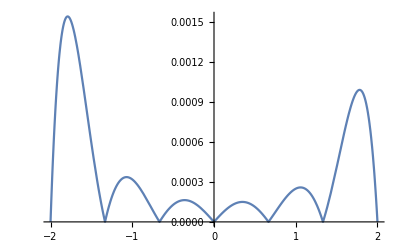

```mathematica
0.0015411738123392027
Plot[Abs[Exp[-x]-nwtn[x]],{x,-2,2}]
```

```mathematica
FindMaximum[{Abs[Exp[-x]-nwtn[x]],-2≤x≤2},{x}]
```

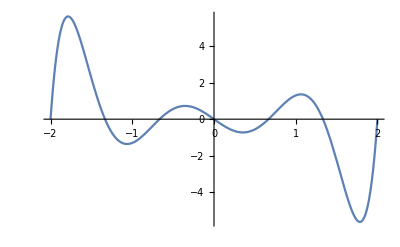

```mathematica
{0.000991586321554827,{2->1.7815914986656485}}
Plot[∏_(i=0)^n (x-xdata[i]),{x,-2,2}]
```

```mathematica
FindMaximum[{∏_(i=0)^n (x-xdata[i]),-2≤x≤2},{x}]
```

```mathematica
{5.609402655125132,{2->-1.7853583936828876}}


ⅇ^2/(7!)×5.609402655125132
```

```mathematica
0.008223847400835345
n1=7
b=2
a=-2
h=(b-a)/n1
XDT={};YDT={};
For[i=0,i≤n1,i++,
xdata1[i]=a+i×h;
ydata1[i]=N[Exp[-xdata1[i]]];
XDT=Append[XDT,xdata1[i]];
YDT=Append[YDT,ydata1[i]];];
Array[xdata1,{n1+1,0}];
Array[ydata1,{n1+1,0}];
MatrixForm[XDT]MatrixForm[YDT]
```

(-2
-10/7
-6/7
-2/7
2/7
6/7
10/7
2) (7.38906
4.17273
2.35642
1.33071
0.751477
0.424373
0.239651
0.135335)

```mathematica
Array[difftab,{n1+1,n1+1},{0,0}];
For[k=1,k≤n1,k++,
For[i=n1,i≥n1-k,i--,difftab[i,k]=""]];
For[i=0,i≤n1,i++,difftab[i,0]=ydata1[i]];
For [k=1, k≤n1,k++,
For[i=0,i≤n1-k,i++,
difftab[i,k]=(difftab[i+1,k-1]-difftab[i,k-1])/(xdata1[i+k]-xdata1[i])]];
tab1 = Array[difftab,{n+1,n1+1}, {0,0}];
PaddedForm[TableForm[tab1],{6,5}]
```

7.38906 | -5.62856 |  2.14376 | -0.54433 |  0.10366 | -0.01579 |  0.00200 | -0.00022
 4.17273 | -3.17855 |  1.21062 | -0.30739 |  0.05854 | -0.00892 |  0.00113 | 
 2.35642 | -1.79499 |  0.68366 | -0.17359 |  0.03306 | -0.00504 |  | 
 1.33071 | -1.01366 |  0.38607 | -0.09803 |  0.01867 |  |  | 
 0.75148 | -0.57243 |  0.21802 | -0.05536 |  |  |  | 
 0.42437 | -0.32326 |  0.12312 |  |  |  |  | 
 0.23965 | -0.18255 |  |  |  |  |  |

```mathematica
(f^(7)(ξ))/7!=-0.00022
ξ=-0.00022*7!
```

(f^7 ξ)/7≠-0.00022

-1.1088

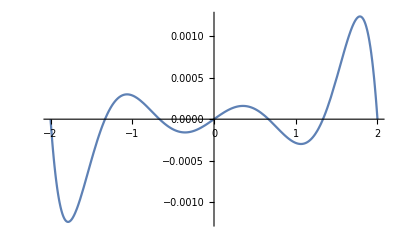

```mathematica
-1.1088
Plot[-0.00022*∏_(i=0)^n (x-xdata[i]),{x,-2,2}]
```

```mathematica
FindMaximum[{-0.00022*∏_(i=0)^n (x-xdata[i]),-2≤x≤2},{x}]
```

```mathematica
{0.0012340685831705096,{2->1.7853509546623016}}
```